## Integration Test

Define a set of functions to be integrated

Define a set of intervals on which `NIntegrate` should be performed

Measure the timing performance of both version of Mathematica

```mathematica
myFunction[k_,a_]:=Sum[i*a*Sin[#]^i,{i,k,0,-1}]&[x];
functionGrupx[n_,a_]:=Table[myFunction[k,a][x],{k,1,n}];
t25=Table[i,{i,1,25,1}];
t55=Table[i,{i,1,50,1}];
t75=Table[i,{i,1,75,1}];
t[ops_]:=Table[i,{i,1,ops,1}];
```

### Create threaded operation

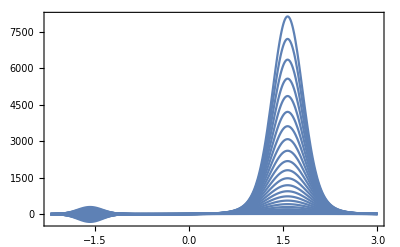

```mathematica
thop[lister_]:=MapThread[myFunction,{lister,lister}];
Plot[thop[t25],{x,-2.2,3},PlotRange->Full,Frame->True,Axes->False]
```

```mathematica
Do[Print[AbsoluteTiming[functionGrupx[100,1]][[1]]],{i,1,10,1}]
```

0.006543

0.006014

0.006207

0.00613

0.006074

0.006069

0.006102

0.006122

0.006137

0.00584

```mathematica
Do[Print[AbsoluteTiming[thop[t[125]]][[1]]],{i,1,10,1}]
```

0.010328

0.010158

0.009397

0.010154

0.010563

0.009969

0.00901

0.010547

0.010058

0.009957

```mathematica
thop[t[2]]
```

{Sin[x],2 Sin[x]+4 Sin[x]^2}